# Si Papi - Cleaned up and Easier to understand

### LH subsystem parameters (Table 1)

```mathematica
v1lh=161(*160.75*)(*Possible Changes*);
kilh=13.6(*13.6*) (*Possible Changes*);
kmlh=47.33(*47.33*)(*Possible Changes*);
clhp=0.98;
clhe=0.9;
dp=1;
dt=0;
de=0;
k=0.92;
δ=1;
𝒶=6.07;
v=2.5;
```

#### LH subsystem parameters that are changed for the Insulin Model

```mathematica
v0lh=33.3(*33.3*) (* Sensitivity to Testosterone*);
```

### FSH subsystem Parameters (Table 2)

```mathematica
vfsh=283.99;
kifsha=6.38;
kifshb=3000;
kfsh=3.41;
cfshp=1.26;
cfshe=0.16;
ζ=0.84;
dinha=1;
dinhb=1;
rfsh=8.21;
```

### Ovarian Subsystem Parameters (Table 3)

```mathematica
c1=0.0871;
c2=0.1251;
c3=0.0533;
c4=0.0371;
c5=0.4813;
d1=0.7053;
d2=0.6488;
k1=0.7089;
k2=0.8712;
k3=1.038;
k4=1.052;
η=1.162;

kmfsh=7.533;
υ=8;
q=0.451;
```

#### Ovarian subsystem parameters that are changed for the Insulin Model (More Research Required)

```mathematica
α=0.71          (*0.71*)(* Dimensionless Parameters that impact Follicle Growth and Total testosterone *);
β=0.6928    (*0.6928*) (* Dimensionless Parameters that impact Follicle Growth and Total testosterone *);
γ=0.0002      (*0.0002*) (* Dimensionless Parameters that impact Follicle Growth and Total testosterone *);
ξ=0.952      (*0.952*)(* Dimensionless Parameters that impact Follicle Growth and Total testosterone *);
```

### Auxiliary equations parameter set (Table 4)

```mathematica
e1=2.3(*2.3*);
e2=2.724(*2.724*);
h0=0.0525;
h1=0.0251(*0.0251*);
h2=0.06315;
h3=0.1584(*0.1584*);
p1=0.2548;
p2=.1276(*0.1276*);
(*InhB levels*)
j1=27.21(*27.21*);
j2=1.885(*1.885*);
j3=3.738;
j4=3.411;
j5=3(*3*);
j6=0.0012;


t2=0.3721;
t3=0.2961;
t4=0.4538;
t5=0.0411;
t6=0.7029;
t7=0.0459;
t8=0.1998;
```

#### Auxiliary equations parameters that are changed for the Insulin Model

```mathematica
t1= 21.92(* 21.92 *)(* Should depend on Insulin, this acts as an intial condition for the auxillary equation*);
e0= 38.25(*38.25*)(* Should depend on Insulin, this acts as an intial condition for the auxillary equation*);
```

#### Metformin Dependant Parameters

```mathematica
mf = 10;

tmf = 1(*0.85714*);
m1mf = 1(*0.3081*);
m2mf = 1(*0.09091*);
m3mf = 1(*0.121212*);
bmf = 1 (*0.7273*) ;
klhmf = 1(*0.67273*);
rlhmf = 1 (*.58*);
```

```mathematica
(*mf = 0;

tmf = 1;
m1mf = 1;
m2mf = 1;
m3mf =1;
bmf = 1 ;
klhmf = 1;
rlhmf = 1;*)
```

### Graphing and Defining Insulin Equations

#### Insulin Data

```mathematica
Meenadata1= {9.36,9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],9.36+RandomReal[{-0.86,0.86}],10.56+RandomReal[{-0.79,0.79}],10.56+RandomReal[{-0.79,0.79}],10.56+RandomReal[{-0.79,0.79}],10.56+RandomReal[{-0.79,0.79}],10.48+RandomReal[{-0.75,0.75}],10.48+RandomReal[{-0.75,0.75}],10.48+RandomReal[{-0.75,0.75}],10.48+RandomReal[{-0.75,0.75}],11.34+RandomReal[{-0.82,0.82}],11.34+RandomReal[{-0.82,0.82}],11.34+RandomReal[{-0.82,0.82}],11.34+RandomReal[{-0.82,0.82}],10.79+RandomReal[{-0.43,0.43}],9.36, 10.79+RandomReal[{-0.43,0.43}]};
MeenadataInsControl=Table[{},29];
For[i=1,i≤ 29, i++,
MeenadataInsControl[[i]]={i,Meenadata1[[i]]}
];

MeenadataInsControlForInterpolation=Table[{},(30/4)+1];
For[i=1,i≤ (30/4)+1, i++,
MeenadataInsControlForInterpolation[[i]]={4i-3,Meenadata1[[4i-3]]}
]
MeenadataInsControlForInterpolation

(* Insulin Data *)
Meenadata21 = {25.29,25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],25.29+RandomReal[{-1.98,1.98}],21.43+RandomReal[{-1.46,1.46}],21.43+RandomReal[{-1.46,1.46}],21.43+RandomReal[{-1.46,1.46}],21.43+RandomReal[{-1.46,1.46}],20.54+RandomReal[{-0.96,0.96}],20.54+RandomReal[{-0.96,0.96}],20.54+RandomReal[{-0.96,0.96}],20.54+RandomReal[{-0.96,0.96}],23.07+RandomReal[{-1.43,1.43}],23.07+RandomReal[{-1.43,1.43}],23.07+RandomReal[{-1.43,1.43}],23.07+RandomReal[{-1.43,1.43}],21.68+RandomReal[{-0.75,0.75}],25.29,21.68+RandomReal[{-0.75,0.75}]};

MeenadataInsPCOS=Table[{},29];
For[i=1,i≤ 29, i++,
MeenadataInsPCOS[[i]]={i,Meenadata21[[i]]}
]

MeenadataInsPCOSForInterpolation=Table[{},(30/4)+1];
For[i=1,i≤ (30/4)+1, i++,
MeenadataInsPCOSForInterpolation[[i]]={4i-3,Meenadata21[[4i-3]]}
]
MeenadataInsPCOSForInterpolation
```

{{1,9.36},{5,9.07002},{9,10.1362},{13,9.83635},{17,10.2193},{21,11.0871},{25,11.4078},{29,9.36}}

{{1,25.29},{5,26.7935},{9,25.0712},{13,24.2317},{17,20.5994},{21,21.4264},{25,22.0499},{29,25.29}}

#### Building Insulin Functions

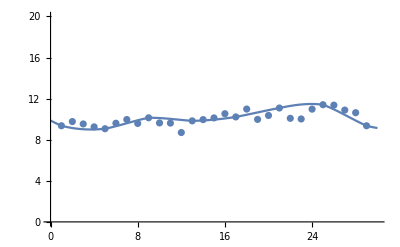

```mathematica
(*Insulin Equation for Normal Insulin Levels*)
InsulinControl=Interpolation[MeenadataInsControlForInterpolation,PeriodicInterpolation->True];
Show[
Plot[InsulinControl[t],{t,0,30},PlotRange -> {0,20}],
ListPlot[MeenadataInsControl]
]
```

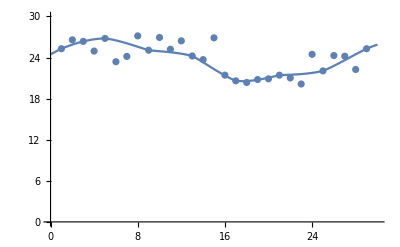

```mathematica
(*Insulin Equation for PCOS Insulin Levels*)
InsulinPCOS=Interpolation[MeenadataInsPCOSForInterpolation, PeriodicInterpolation->True];
Show[
Plot[InsulinPCOS[t],{t,0,30},PlotRange -> {0,30}],
ListPlot[MeenadataInsPCOS]
]
```

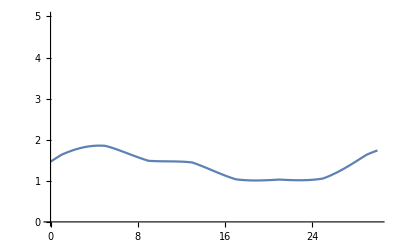

```mathematica
InsulinRatio[t_] := (InsulinPCOS[t]-mf)/InsulinControl[t]
Show[
Plot[InsulinRatio[t],{t,0,30},PlotRange -> {0,5}]
]
```

```mathematica
AvGIns = Table[{},29]

For[i=1, i<= 29, i++,
AvGIns[[i]]=Evaluate[InsulinRatio[i]]
]
AvGIns

AvG = Sum[AvGIns[[i]]/29,{i,1,29}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

{1.63355,1.73847,1.81277,1.85138,1.85154,1.77171,1.67422,1.57505,1.48686,1.47608,1.47281,1.46663,1.44684,1.34694,1.23672,1.12933,1.0372,1.01334,1.00843,1.01613,1.0306,1.01785,1.01379,1.02442,1.05628,1.16683,1.30635,1.46658,1.63355}

1.37111

#### Parameters that I actually changed

```mathematica
(*Tesosterone Initial Condition*)
t1= 21.92*(2.375/2.75)^(1-mf/15)(*0.85714*)(* 21.92 *)(* Should depend on Insulin this acts as an intial condition for the auxillary equation*);

(*How the Follicle Mass is exchanged through the cycle*)
m1=0.9274*((.8626267)/2.75)^(1-mf/15)(*0.80 *)(*0.9274*) (*primordial follicle recruitment*);
m2=1.338*(10^(-3))*(0.25/2.75)^(1-mf/15)(**0.25*)(*1.338*(10^(-3))*);
m3=.15*(0.3333333/2.75)^(1-mf/15)(*0.05*);
b=0.0189*(2/2.75)^(1-mf/15)(**2*);

(*How LH is Released From the Brain and LH equations *)
klh=20*(1.85/2.75)^(1-mf/15)(**1.85*) (*19.99*)(* Rate at which the The Brain Releases LH *);
rlh=14*(1.5/2.75)^(1-mf/15)(*1.5*)(*Rate at which LH is released from the LH equation*);
```

### Differential Equations in the Ovaries

#### Follicle Recruitment and Growth

```mathematica
DEF1= D[pra1[t],t]==m1*m1mf*InsulinRatio[t]-m2*m2mf*InsulinRatio[t]*T[t]^(η)*pra1[t]*pra2[t];
DEF2=D[pra2[t],t]==(m2*m2mf*InsulinRatio[t]*T[t]^(η)*pra1[t]*pra2[t]-m3*m3mf *InsulinRatio[t]*(fsh[t]^(υ)/(kmfsh^(υ)+fsh[t]^(υ)))*pra2[t]*sman[t]);
DEF3=D[sman[t],t]==(m3*m3mf *InsulinRatio[t]*(fsh[t]^(υ)/(kmfsh^(υ)+fsh[t]^(υ)))*pra2[t]*sman[t]-b*bmf*InsulinRatio[t]*fsh[t]^(q)*sman[t]*rcf[t]);
```

#### Development of the Primary Follicle

```mathematica
DEF4= D[rcf[t],t]==(b*bmf*InsulinRatio[t]*fsh[t]^(q)*sman[t]*rcf[t]+(c1*fsh[t]-c2*lh[t]^(α))*rcf[t]);
DEF5= D[dmf[t],t]==( (c2*lh[t]^(α)*rcf[t])+(c3*lh[t]^(β)-c4*lh[t]^(ξ))*dmf[t]); 
DEF6= D[ovf[t],t]== (c4*lh[t]^(ξ)*dmf[t]-c5*lh[t]^(γ)*ovf[t]);
```

#### After Ovulation: Development of the Corpus Luteum

```mathematica
DEF7= D[cl1[t],t]==c5*lh[t]^(γ)*ovf[t]-d1*cl1[t];
DEF8= D[cl2[t],t]== d1*cl1[t]-d2*cl2[t];
```

#### After Ovulation: Regression of the Corpus Luteum

```mathematica
DEF9= D[lut1[t],t]== d2*cl2[t]-k1*lut1[t];
DEF10= D[lut2[t],t]== k1*lut1[t]-k2*lut2[t];
DEF11= D[lut3[t],t]== k2*lut2[t]-k3*lut3[t];
DEF12= D[lut4[t],t]== k3*lut3[t]-k4*lut4[t];
```

### Auxiliary Equations

```mathematica
(*Estrogen*)
E2[t_]:=e0+e1*dmf[t]+e2*lut4[t];

(*Progesterone*)
P4[t_]:=p1*lut3[t]+p2*lut4[t];

(*INhibin A & B*)
InhA[t_]:=h0+h1*ovf[t]+h2*lut2[t]+h3*lut3[t];
InhB[t_]:=j1+j2*pra2[t]+j3*sman[t]+j4*rcf[t]+j5*cl1[t]^(j6);

(*Testosterone*)
T[t_]:=t1*tmf*InsulinRatio[t]+t2*pra2[t]+t3*sman[t]+t4*rcf[t]+t5*dmf[t]+t6*ovf[t]+t7*lut1[t]+t8*lut3[t];
```

### Differential Equations from the Brain

#### Brain Synthesis of LH and FSH

```mathematica
(*Represent the amounts of gonadotrophin synthesized in the pituitary via GnRH and the state of LH represent blood constrations*)
DEF13= D[rplh[t],t]== (v0lh*T[t-dt]^(k)+v1lh*((E2[t-de]^(𝒶))/(kmlh^(𝒶)+E2[t-de]^(𝒶))))/(1+(P4[t-dp]/kilh))-(klh*klhmf*InsulinRatio[t]*((1+clhp*P4[t]^(δ))/(1+clhe*E2[t]))*rplh[t]) ;

(*Represent the amounts of gonadotrophin synthesized in the pituitary via GnRH and the state of FSH represent blood constrations*)
DEF15= D[rpfsh[t],t]== vfsh/(1+(InhA[t-dinha]/kifsha)+(InhB[t-dinhb]/kifshb))-kfsh*((1+cfshp*P4[t])/(1+cfshe*E2[t]^(ζ)))*rpfsh[t];
```

#### Released LH and FSH to the Ovaries

```mathematica
DEF14= D[lh[t],t]== (1/v)*klh*klhmf*InsulinRatio[t]*((1+clhp*P4[t]^(δ))/(1+clhe*E2[t]))*rplh[t]-rlh*rlhmf*InsulinRatio[t]*lh[t];
DEF16= D[fsh[t],t]== (1/v)*kfsh*((1+cfshp*P4[t])/(1+cfshe*E2[t]^(ζ)))*rpfsh[t]-rfsh*fsh[t];
```

## Solving Differential Equations

```mathematica
SIRsys={DEF1,DEF2,DEF3, DEF4, DEF5,DEF6,DEF7,DEF8,DEF9,DEF10,DEF11,DEF12,DEF13,DEF14,DEF15,DEF16};

(*Subject to change if it is believed to be affected by Insulin*)
initial={pra1[0]==0.6112,pra2[0]==15.11+3,sman[0]==12.36+3,rcf[0]== 0.1511,dmf[0]== 1.337,ovf[0]==1.168,cl1[0]==1.003,cl2[0]==1.865,lut1[0]==3.265,lut2[0]==4.071,lut3[0]==6.055,lut4[0]==9.029,rplh[0]==1071,lh[0]== 20(*36*).0,rpfsh[0]==155.6,fsh[0]==11.40};

solution=Flatten[NDSolve[Join[SIRsys,initial],{pra1,pra2,sman,rcf, dmf,ovf,cl1,cl2,lut1,lut2,lut3,lut4,rplh,lh,rpfsh,fsh},{t,0,360}]]

(*Defining the Solutions*)
eqn1s = Evaluate[pra1/.solution[[1]]];
eqn2s = Evaluate[pra2/.solution[[2]]];
eqn3s = Evaluate[sman/.solution[[3]]];
eqn4s = Evaluate[rcf/.solution[[4]]];
eqn5s = Evaluate[dmf/.solution[[5]]];
eqn6s = Evaluate[ovf/.solution[[6]]];
eqn7s = Evaluate[cl1/.solution[[7]]];
eqn8s = Evaluate[cl2/.solution[[8]]];
eqn9s = Evaluate[lut1/.solution[[9]]];
eqn10s = Evaluate[lut2/.solution[[10]]];
eqn11s = Evaluate[lut3/.solution[[11]]];
eqn12s = Evaluate[lut4/.solution[[12]]];
eqn13s = Evaluate[rplh/.solution[[13]]];
eqn14s = Evaluate[lh/.solution[[14]]];
eqn15s = Evaluate[rpfsh/.solution[[15]]];
eqn16s = Evaluate[fsh/.solution[[16]]];
```

NDSolve::ihist: Conditions given at t = 0. will be interpreted as initial history functions for t/;t≤0..

{pra1→InterpolatingFunction[{{0., 360.}}, <>],pra2→InterpolatingFunction[{{0., 360.}}, <>],sman→InterpolatingFunction[{{0., 360.}}, <>],rcf→InterpolatingFunction[{{0., 360.}}, <>],dmf→InterpolatingFunction[{{0., 360.}}, <>],ovf→InterpolatingFunction[{{0., 360.}}, <>],cl1→InterpolatingFunction[{{0., 360.}}, <>],cl2→InterpolatingFunction[{{0., 360.}}, <>],lut1→InterpolatingFunction[{{0., 360.}}, <>],lut2→InterpolatingFunction[{{0., 360.}}, <>],lut3→InterpolatingFunction[{{0., 360.}}, <>],lut4→InterpolatingFunction[{{0., 360.}}, <>],rplh→InterpolatingFunction[{{0., 360.}}, <>],lh→InterpolatingFunction[{{0., 360.}}, <>],rpfsh→InterpolatingFunction[{{0., 360.}}, <>],fsh→InterpolatingFunction[{{0., 360.}}, <>]}

### Creating Graphs of Solutions

```mathematica
pra1plot = Plot[eqn1s[t],{t,0,120},PlotStyle->{RGBColor[.25,0,0]},DisplayFunction->Identity, PlotLegends->Placed[{"Preantral Follicle 1"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
pra2plot = Plot[eqn2s[t],{t,0, 120},PlotStyle->{RGBColor[.5,0,0],Dashed},DisplayFunction->Identity, PlotLegends->Placed[{"preantral follicle 2"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
smanplot = Plot[eqn3s[t],{t,0,120},PlotStyle->{RGBColor[.75,0,0],Dotted},DisplayFunction->Identity, PlotLegends->Placed[{"small antral follicle"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
rcfplot = Plot[eqn4s[t],{t,0,120},PlotStyle->{RGBColor[0,1,0]},DisplayFunction->Identity, PlotLegends->Placed[{"RcF"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
dmfplot = Plot[eqn5s[t],{t,0,120},PlotStyle->{RGBColor[0,.25,0]},DisplayFunction->Identity, PlotLegends->Placed[{"DmF"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
ovfplot = Plot[eqn6s[t],{t,0,120},PlotStyle->{RGBColor[0,.75,0]},DisplayFunction->Identity, PlotLegends->Placed[{"OvF"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
cl1plot = Plot[eqn7s[t],{t,0,120},PlotStyle->{RGBColor[0,0,1]},DisplayFunction->Identity, PlotLegends->Placed[{"CL1"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
cl2plot = Plot[eqn8s[t],{t,0,120},PlotStyle->{RGBColor[0,0,.5],Dashed},DisplayFunction->Identity, PlotLegends->Placed[{"CL2"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
lut1plot = Plot[eqn9s[t],{t,0,120},PlotStyle->{RGBColor[0,1,1]},DisplayFunction->Identity, PlotLegends->Placed[{"Lut1"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
lut2plot = Plot[eqn10s[t],{t,0,120},PlotStyle->{RGBColor[0,.75,1],Dashed},DisplayFunction->Identity, PlotLegends->Placed[{"Lut2"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
lut3plot = Plot[eqn11s[t],{t,0,120},PlotStyle->{RGBColor[0,.5,1],Dotted},DisplayFunction->Identity, PlotLegends->Placed[{"Lut3"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
lut4plot = Plot[eqn12s[t],{t,0,120},PlotStyle->{RGBColor[0,.25,1]},DisplayFunction->Identity, PlotLegends->Placed[{"Lut4"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
rplhplot = Plot[eqn13s[t],{t,0,120},PlotStyle->{RGBColor[1,.75,1],Dashed},DisplayFunction->Identity, PlotLegends->Placed[{"RpLH"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
lhplot = Plot[eqn14s[t],{t,0,120},PlotStyle->Green,DisplayFunction->Identity, PlotLegends->Placed[{"LH"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
rpfshplot = Plot[eqn15s[t],{t,0,120},PlotStyle->{RGBColor[1,.25,1],Dashed},DisplayFunction->Identity, PlotLegends->Placed[{"RpFSH"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->All];
fshplot = Plot[eqn16s[t],{t,0,120},PlotStyle->{Red},DisplayFunction->Identity, PlotLegends->Placed[{"FSH"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->{0,25}];
```

### Graphing Equations Accordingly (Within Each “System”)

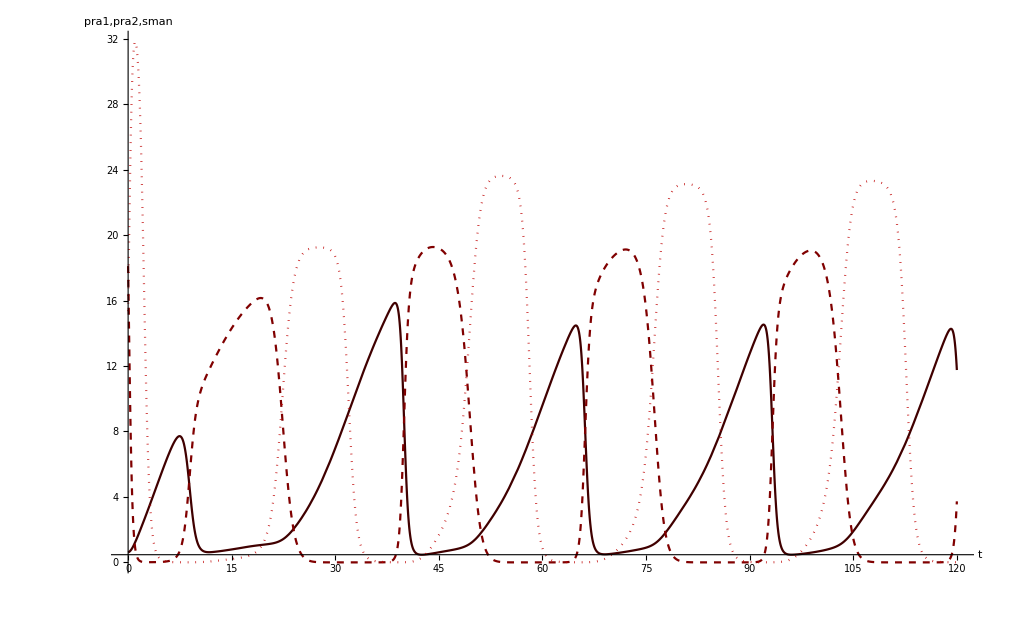

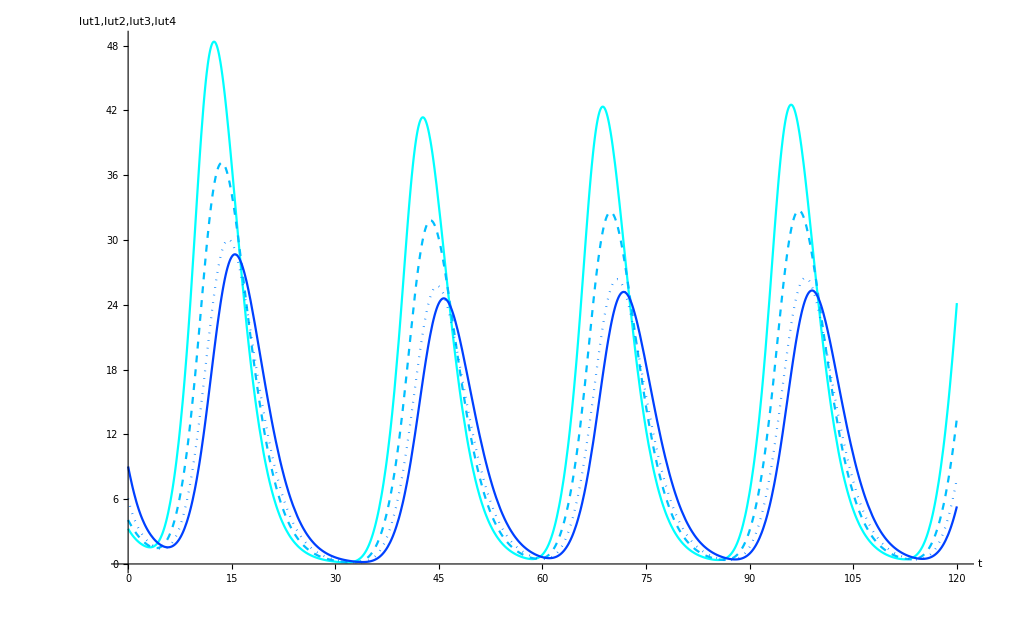

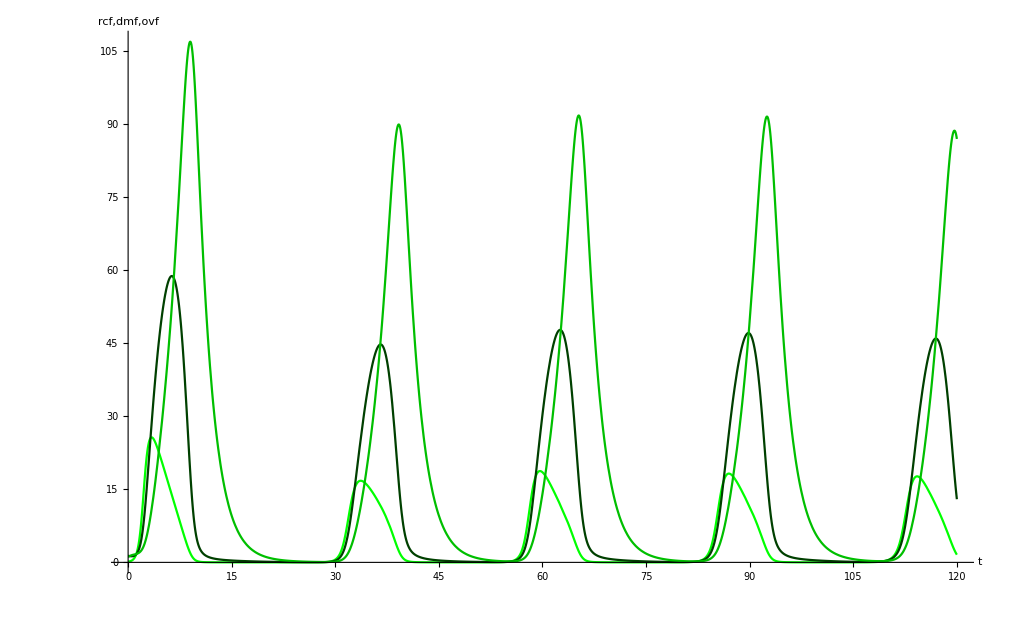

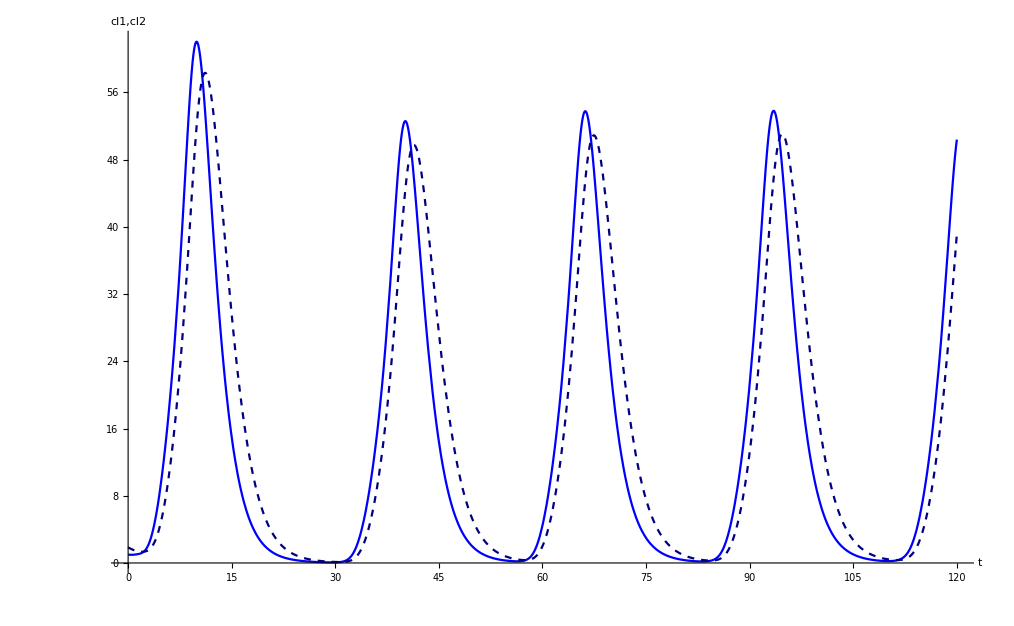

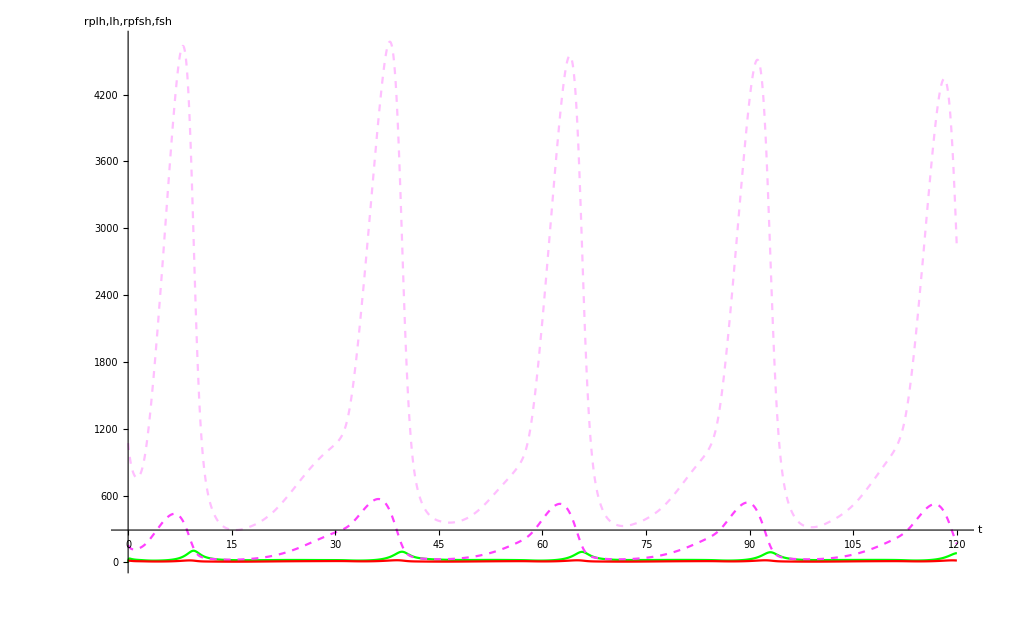

```mathematica
Show[pra1plot,pra2plot,smanplot, AxesLabel->{"t","pra1,pra2,sman"},DisplayFunction->$DisplayFunction,PlotRange->All]
Show[lut1plot,lut2plot,lut3plot,lut4plot,  AxesLabel->{"t","lut1,lut2,lut3,lut4"},DisplayFunction->$DisplayFunction,PlotRange->All]
Show[rcfplot,dmfplot,ovfplot,  AxesLabel->{"t","rcf,dmf,ovf"},DisplayFunction->$DisplayFunction,PlotRange->All]
Show[cl1plot,cl2plot,  AxesLabel->{"t","cl1,cl2"},DisplayFunction->$DisplayFunction,PlotRange->All]
Show[rplhplot,lhplot,rpfshplot, fshplot,  AxesLabel->{"t","rplh,lh,rpfsh,fsh"},DisplayFunction->$DisplayFunction,PlotRange->All]
```

## Data For Regular People

```mathematica
xval = Table[{},30];
For[i=1,i≤ Length[xval], i++,
xval[[i]] =  i 
];
LHn = 3;

(* FSH data from Hendrix paper *)
henFSH={11.4, 11.6, 11.7, 12.8,13, 11.3, 12.1, 11.3, 10, 8.8, 8.7, 8.3,10.3, 19.6, 12.2, 9.3, 8.7, 8.6, 7.4, 7.2, 6.1, 5.5, 5.3,5.5,5.4, 6.1, 6.8, 8.4, 11.4, 11.6, 11.7, 12.4, 12.6, 11.3, 12.1, 11.3, 10, 8.7, 8.6, 8.2, 10.4, 19.6, 12.2, 9.2, 8.7, 8.6, 7.4, 7.2, 6.1, 5.4, 5.2, 5.4, 5.3, 6.1, 6.7, 8.3, 11.3, 11.6, 11.7, 12.4};

Fdata=Table[{},Length[xval]];

For[i=1,i≤ Length[xval]-(LHn-1), i++,
Fdata[[i]] =  {xval[[i]],henFSH[[i+LHn]]} 
];

For[i=1,i≤ LHn-1, i++,
Fdata[[i+Length[xval]-(LHn-1)]] =  {xval[[i+ Length[xval]-(LHn-1)]],henFSH[[i]]} 
];
FdataPlot = ListPlot[Fdata,PlotStyle -> Red];



henLH={12,14,16,15,17,17,19,18,17,16,17,26,50,133,42,22,20,20,17,16,13,9,12,11,12,12,12,13,14,15,17,16,18,18,20,19,18,17,17,26,50,133,42,22,20,20,18,16,13,10,12, 11, 12, 12, 12, 13, 14, 15, 17,16};
Ldata= Table[{},Length[xval]];

For[i=1,i≤ Length[xval]-(LHn-1), i++,
Ldata[[i]] =  {xval[[i]],henLH[[i+LHn]]} 
]
For[i=1,i≤ LHn-1, i++,
Ldata[[i+Length[xval]-(LHn-1)]] =  {xval[[i+ Length[xval]-(LHn-1)]],henLH[[i]]} 
]
LdataPlot=ListPlot[Ldata, PlotStyle -> Green];


(* InhA data from Hendrix paper *)
henInhA={1,1.2,1,1.2,1.2,1,1.2,1.3,1.8,2.3,3.3,4.5,7.4,9.3,7.8,8.1,10.1,8.9,9.4,11.7,9.2,8.8,7.6,6.8,5.9,4.3,2.3,1.9,1,1.2,1,1.2,1.2,1,1.2,1.3,1.8,2.3,3.3,4.5,7.4,9.3,7.8,8.1,10.1,8.9,9.4,11.7,9.2,8.8,7.6,6.8,5.9,4.3,2.3,1.9,1,1.2,1,1.2};
InhAdata=Table[{},30];
For[i=1,i≤ 30, i++,InhAdata[[i]]={i,henInhA[[i+LHn]]}]
InhAdataPlot=ListPlot[InhAdata, PlotStyle -> Magenta];


(* InhB data from paper *)
henInhB={76,110,120,123,140,135,140,145,148,127,112,98,77,148,165,105,55,47,46,40,30,28,27,40,30,40,38,55,76,110,120,123,140,135,140,145,148,127,112,98,77,148,165,105,55,47,46,40,30,28,27,40,30,40,38,55,76,110,120,123};
InhBdata=Table[{},30];
For[i=1,i≤ 30, i++,InhBdata[[i]]={i,henInhB[[i+LHn]]}]
InhBdataPlot=ListPlot[InhBdata, PlotStyle -> Purple];


(* E2 data from Hendrix Paper *)
henE2={50,55,53,58,60,63,68,72,95,115,135,189,230,215,125,90,105,120,145,130,154,145,140,155,130,115,65,55,50,55,53,58,60,63,68,72,95,115,135,189,230,215,125,90,105,120,145,130,154,145,140,155,130,115,65,55,50,55,53,58};
E2data=Table[{},30];
For[i=1,i≤ 30, i++,E2data[[i]]={i,henE2[[i+LHn+1]]}]
E2dataPlot=ListPlot[E2data, PlotStyle -> Blue];


(* P4 data from Hendrix Paper *)
henP4={1.2,1,1,1,1,1,1,1,1,1,1,1,1.1,1.25,2,5,8.75,11.2,16,17.5,17.8,17.3,14,12.5,11,9,4,1.8,1.2,1,1,1,1,1,1,1,1,1,1,1,1.1,1.25,2,5,8.75,11.2,16,17.5,17.8,17.3,14,12.5,11,9,4,1.8,1.2,1,1,1};
P4data=Table[{},30];
For[i=1,i≤ 30, i++,P4data[[i]]={i,henP4[[i+LHn+1]]}]
P4dataPlot=ListPlot[P4data, PlotStyle -> Black];


(* T data from Hendrix {converted units of Sinha-Hikim} *)
henT={33,31,36,43,40,35,34,31,34};
Tdata={{0,33},{3,31},{6,36},{9,43},{12,40},{15,35},{18,34},{21,31},{24,34}};
TdataPlot=ListPlot[Tdata, PlotStyle -> RGBColor[.3,.7,0]];
```

## Data for PCOS Victims

```mathematica
(* Progesterone data *)
Meenadata22 = {1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],1.74+RandomReal[{-0.433,0.433}],4.06+RandomReal[{-1.92,1.92}],4.06+RandomReal[{-1.92,1.92}],4.06+RandomReal[{-1.92,1.92}],4.06+RandomReal[{-1.92,1.92}],5.50+RandomReal[{-4.07,4.07}],5.50+RandomReal[{-4.07,4.07}],5.50+RandomReal[{-4.07,4.07}],5.50+RandomReal[{-4.07,4.07}],5.13+RandomReal[{-3.16,3.16}],5.13+RandomReal[{-3.16,3.16}],5.13+RandomReal[{-3.16,3.16}],5.13+RandomReal[{-3.16,3.16}],4.90+RandomReal[{-1.75,1.75}],4.90+RandomReal[{-1.75,1.75}],4.90+RandomReal[{-1.75,1.75}],4.90+RandomReal[{-1.75,1.75}]};

MeenadataP4PCOS=Table[{},30];
For[i=1,i≤ 30, i++,
MeenadataP4PCOS[[i]]={i,Meenadata22[[i]]}
]

(* LH data *)
Meenadata23 = {24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],24.37+RandomReal[{-1.98,1.98}],28.37+RandomReal[{-0.99,0.99}],28.37+RandomReal[{-0.99,0.99}],28.37+RandomReal[{-0.99,0.99}],28.37+RandomReal[{-0.99,0.99}],22.11+RandomReal[{-1.25,1.25}],22.11+RandomReal[{-1.25,1.25}],22.11+RandomReal[{-1.25,1.25}],22.11+RandomReal[{-1.25,1.25}],14.57+RandomReal[{-1.36,1.36}],14.57+RandomReal[{-1.36,1.36}],14.57+RandomReal[{-1.36,1.36}],14.57+RandomReal[{-1.36,1.36}],21.69+RandomReal[{-1.43,1.43}],21.69+RandomReal[{-1.43,1.43}],21.69+RandomReal[{-1.43,1.43}],21.69+RandomReal[{-1.43,1.43}]};

MeenadataLHPCOS=Table[{},30];
For[i=1,i≤ 30, i++,
MeenadataLHPCOS[[i]]={i,Meenadata23[[i]]}
]
```

## Graphing Plots against Data

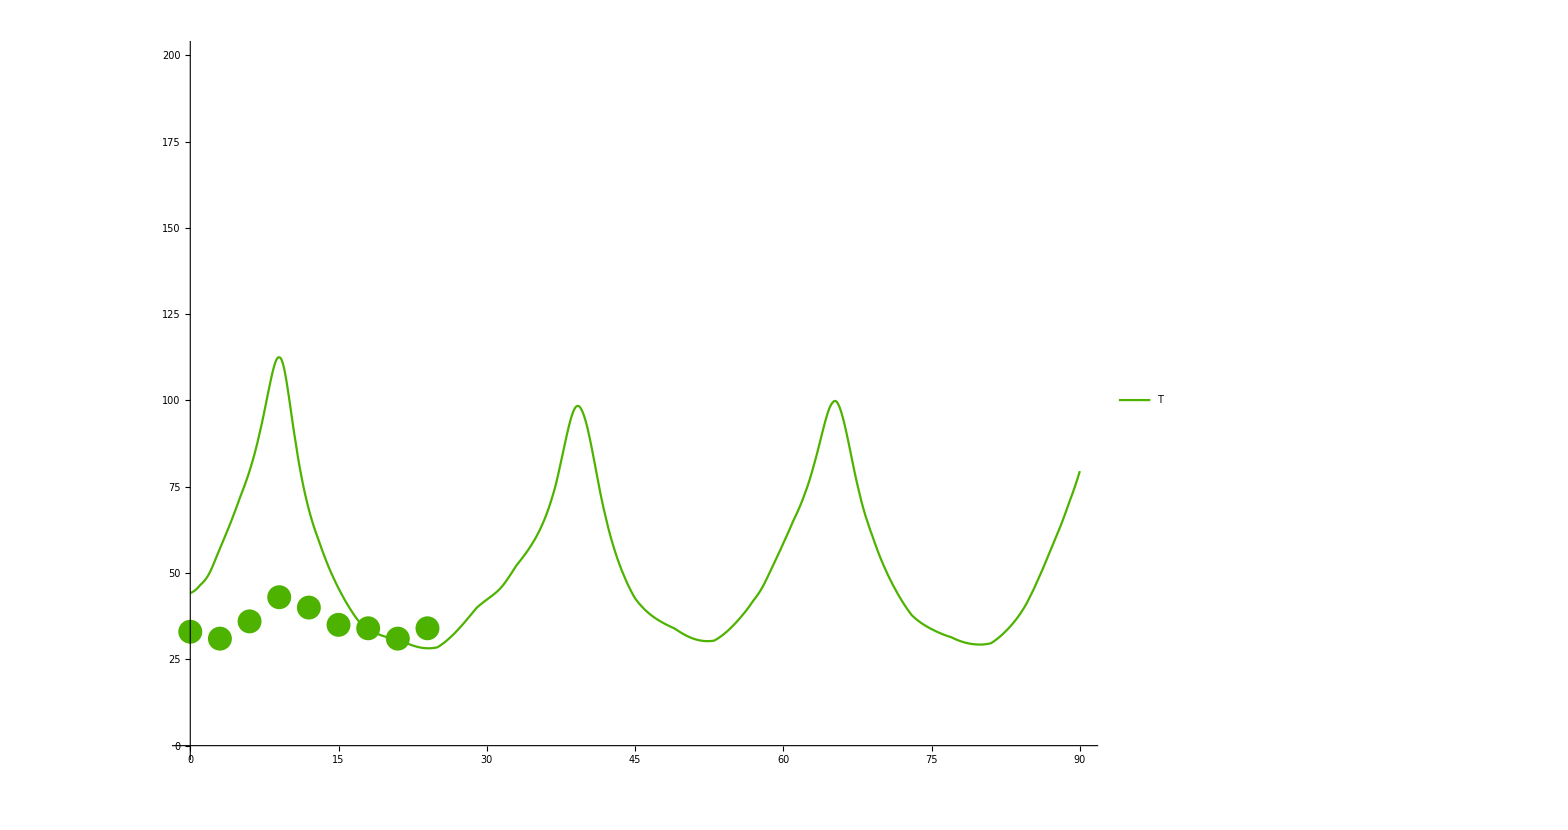

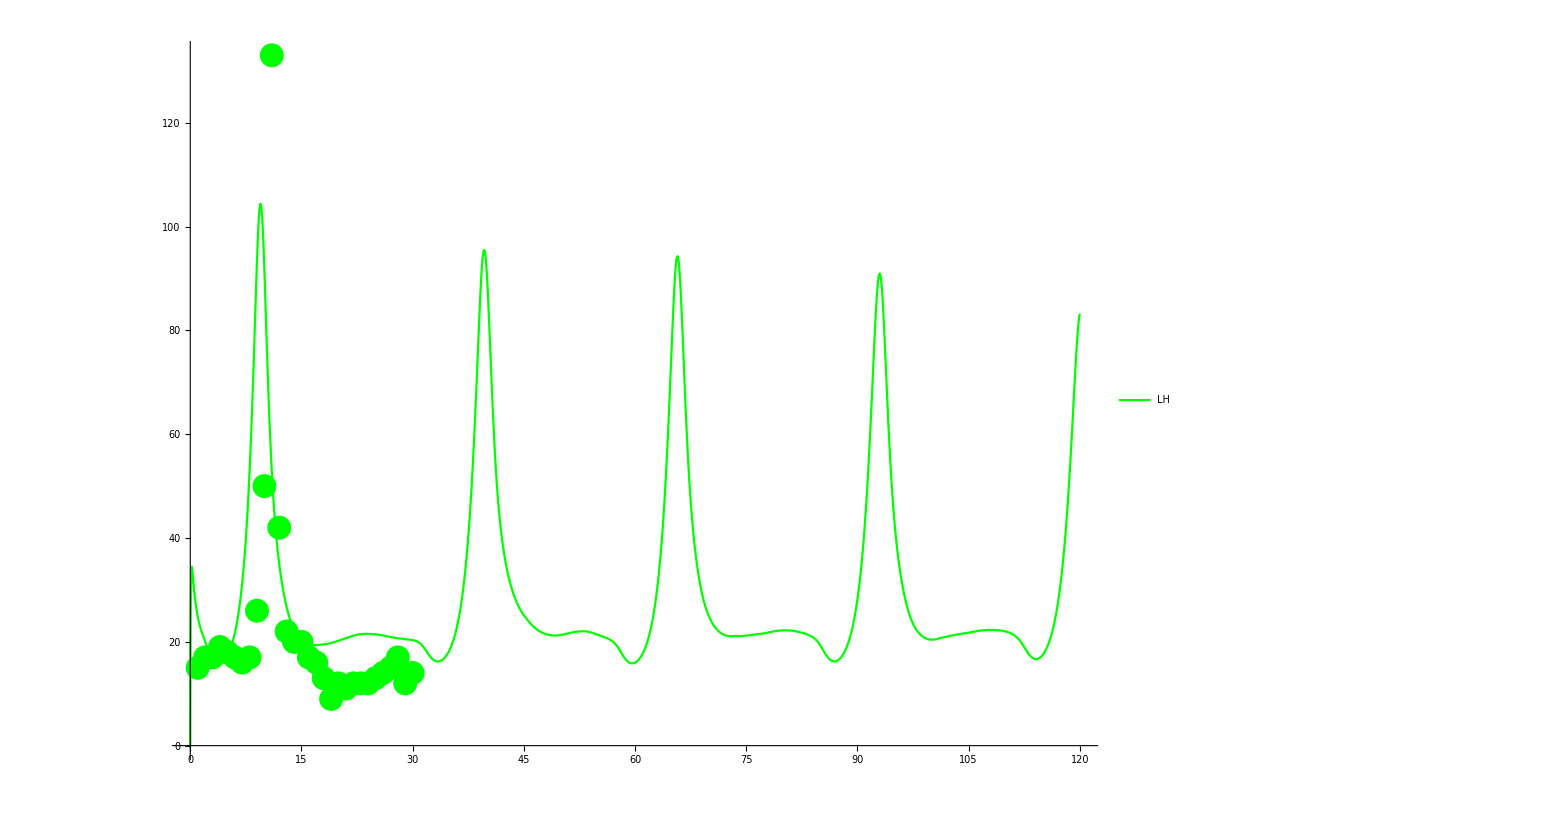

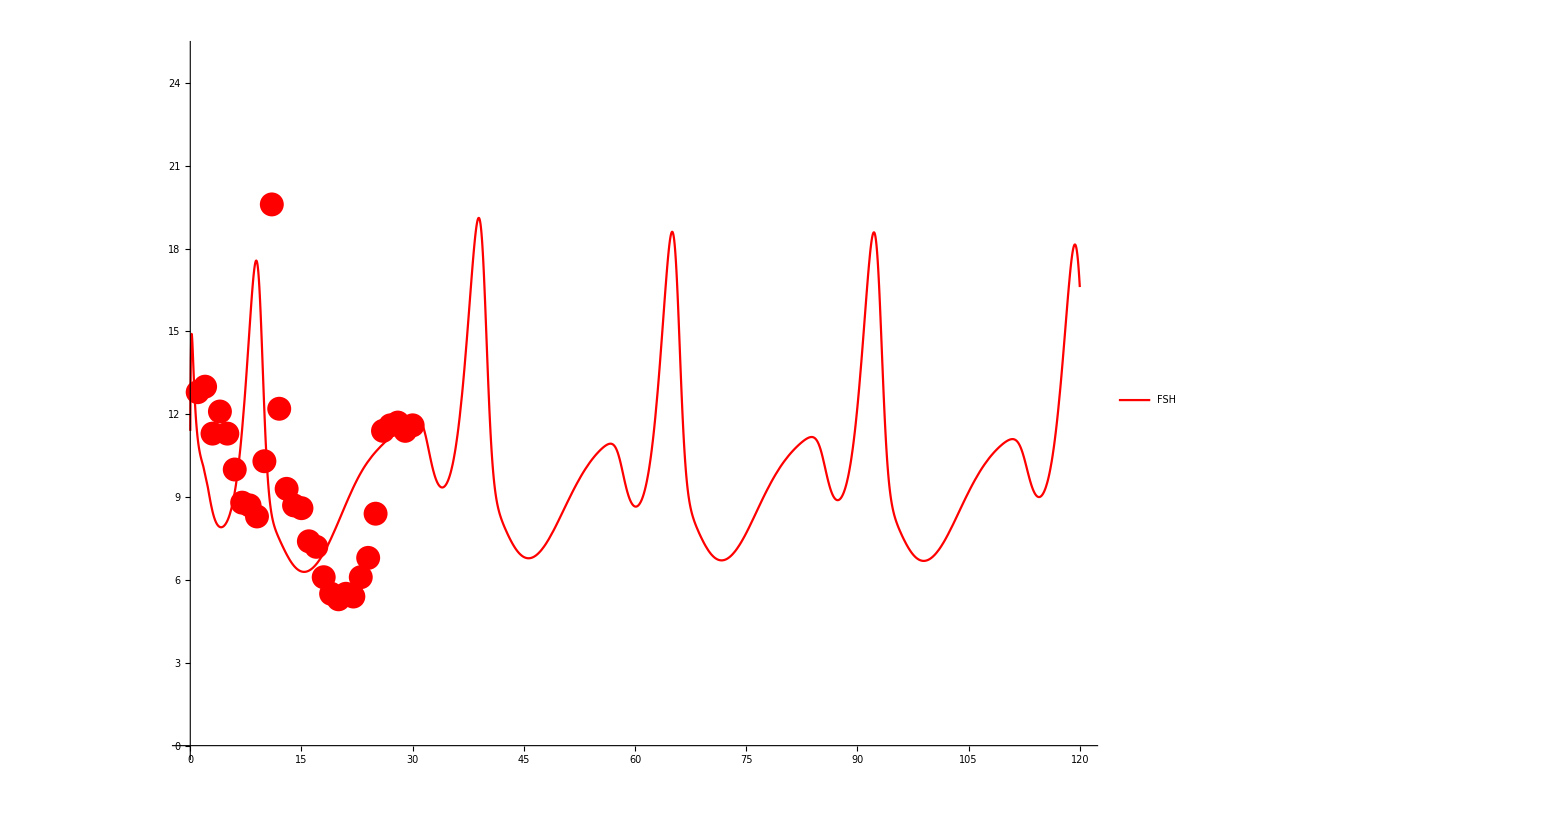

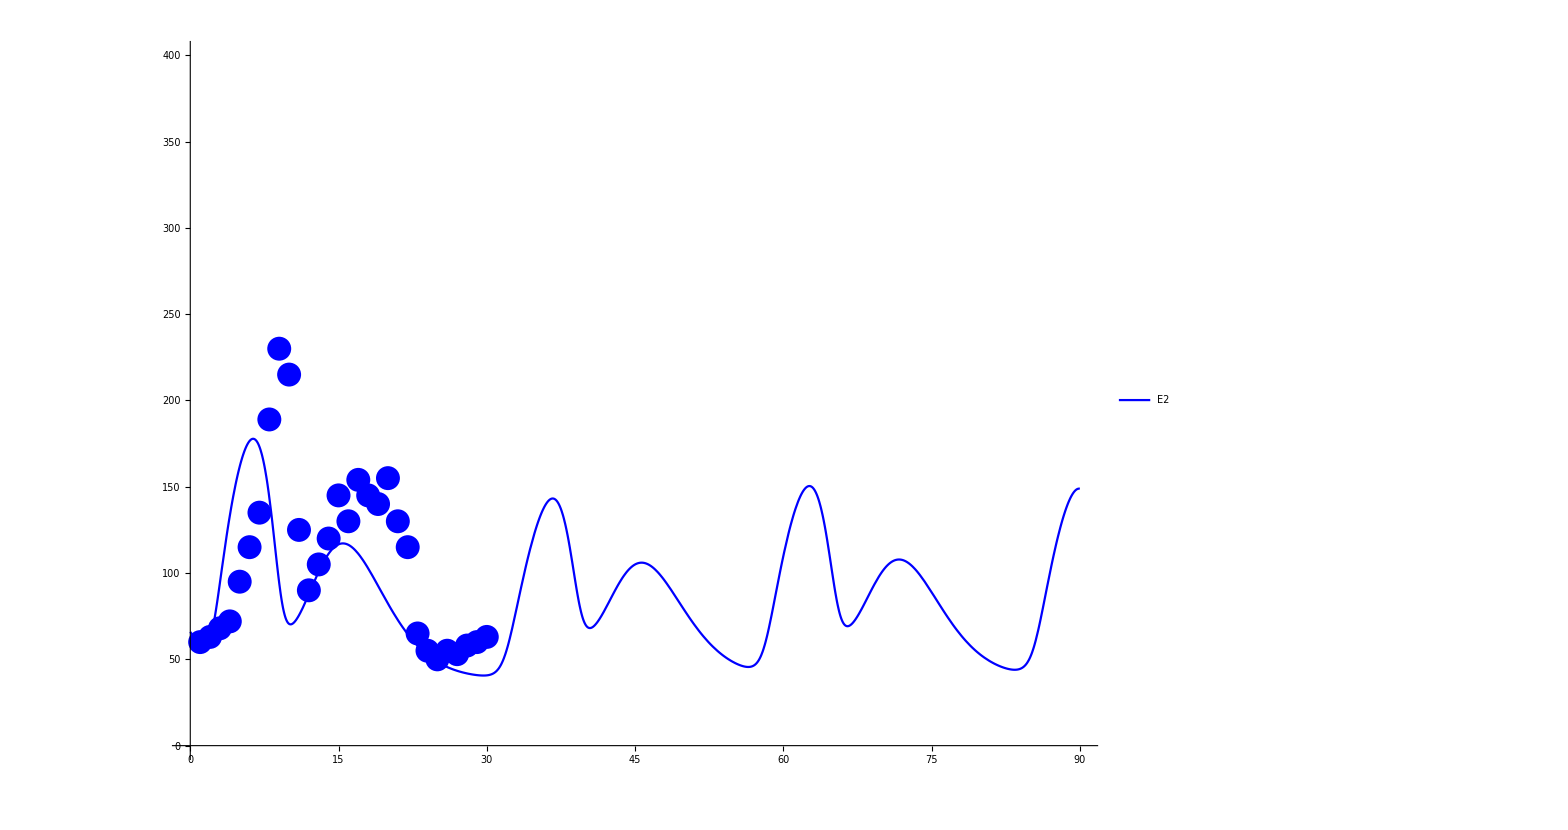

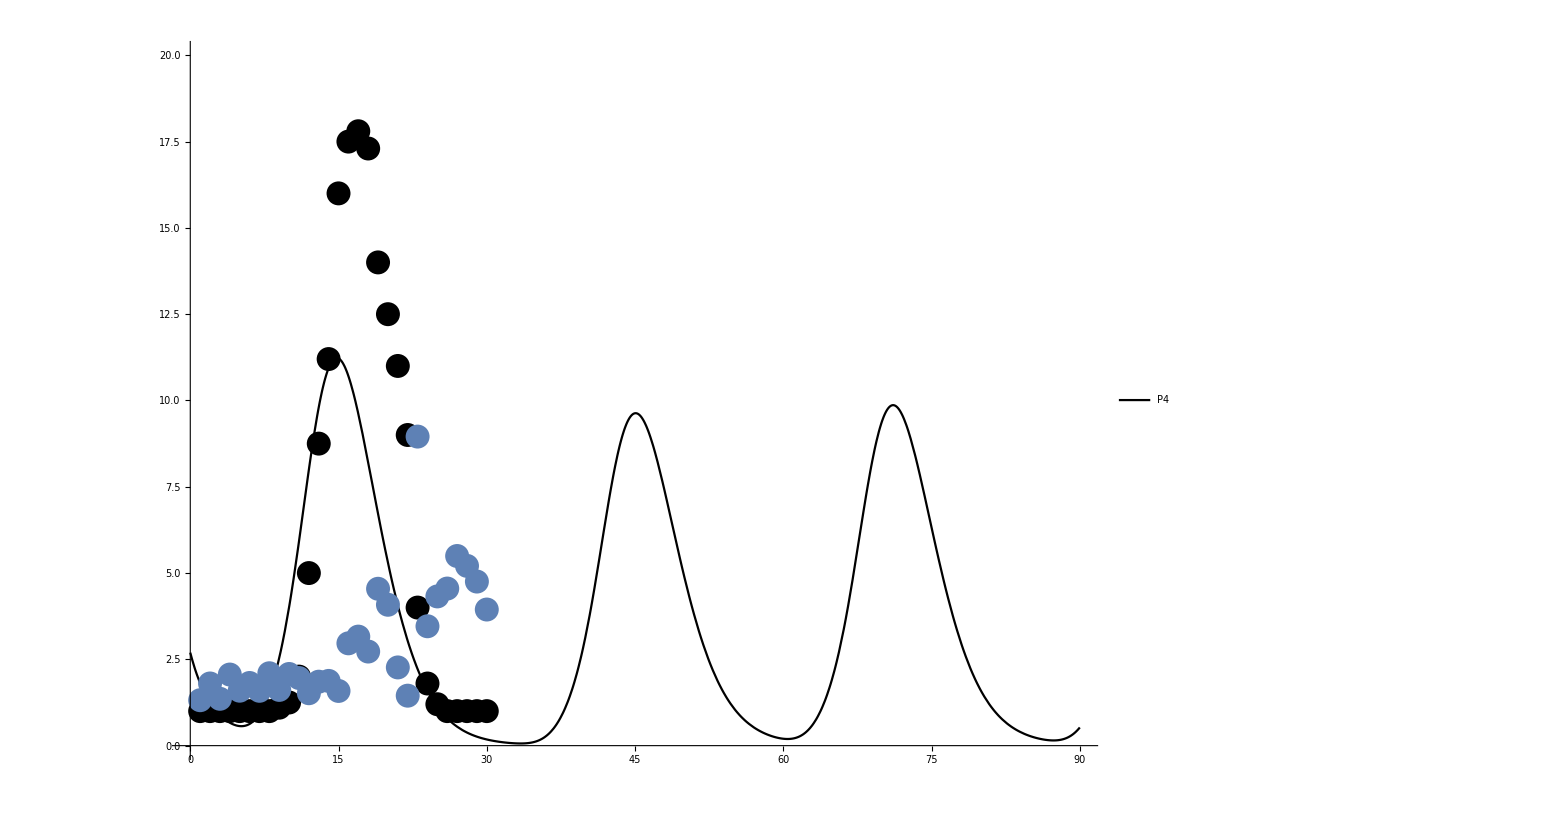

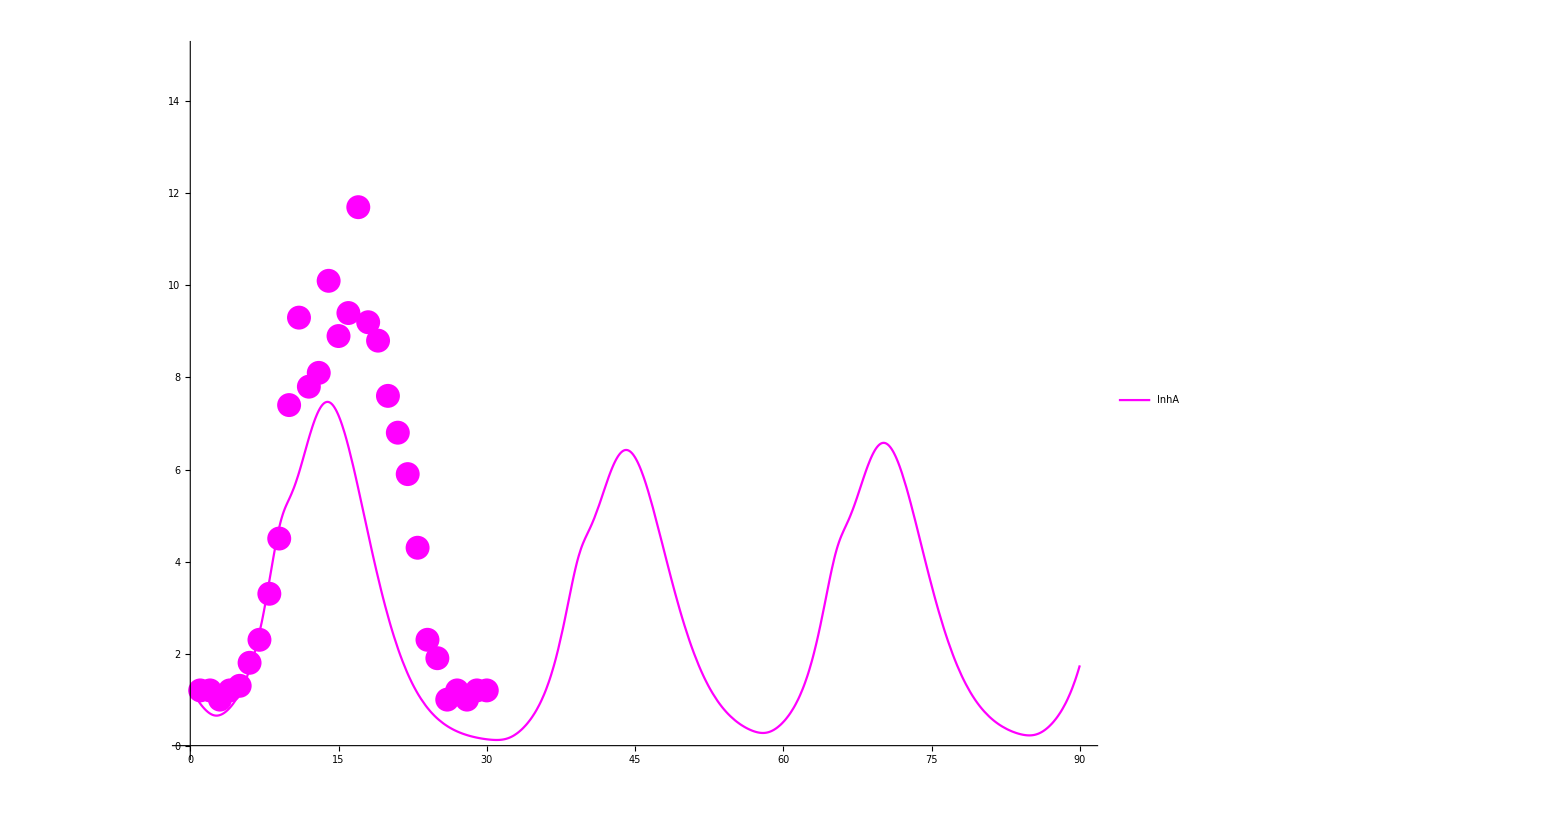

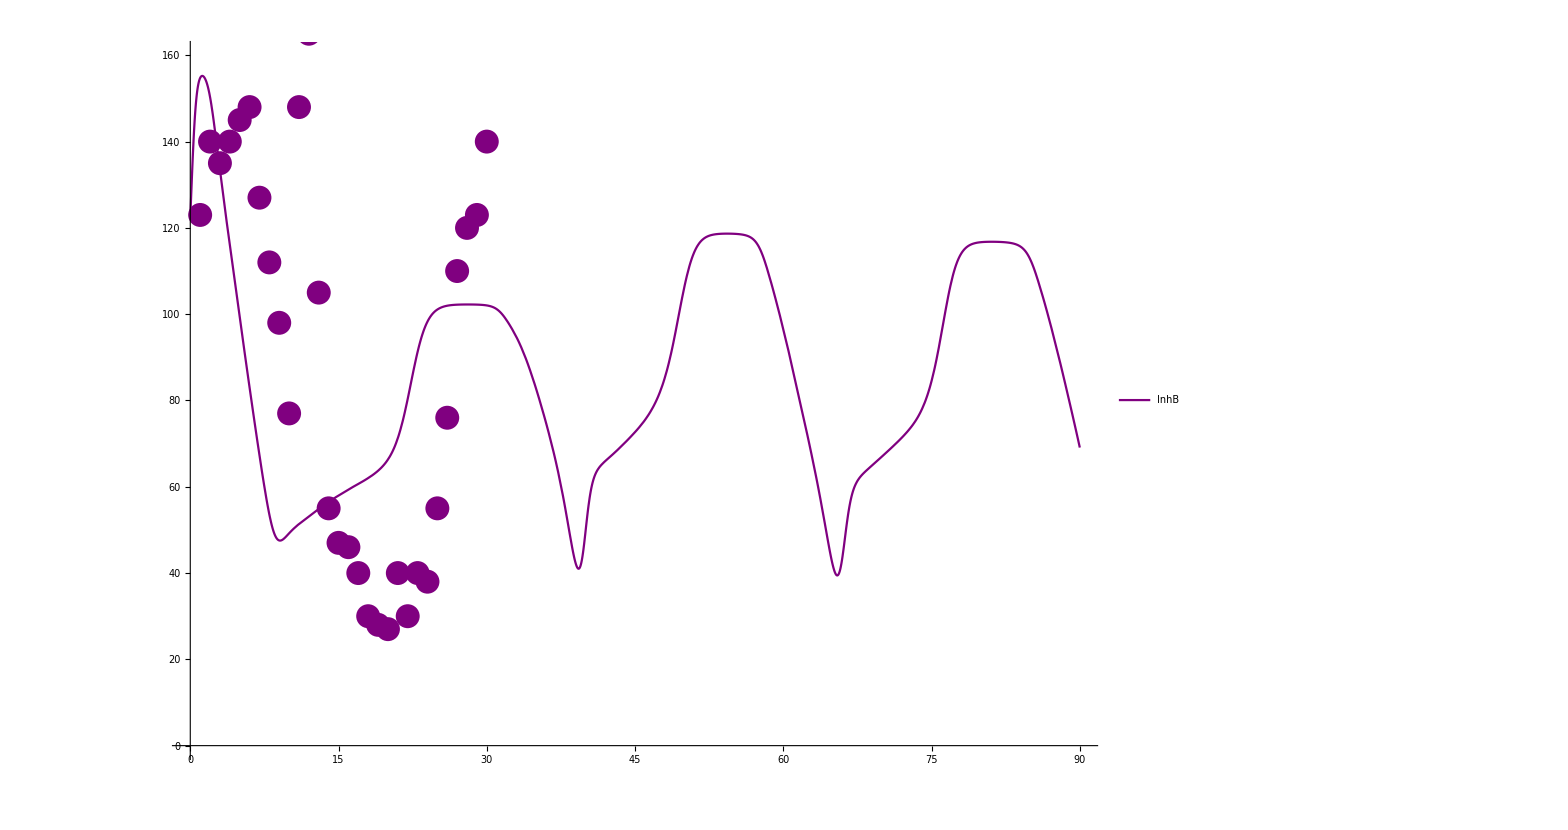

```mathematica
(*Testosterone A For Normal People*)
Show[
Tplot = Plot[Evaluate[T[t]/.solution],{t,0,90},PlotStyle->{RGBColor[.3,.7,0]},DisplayFunction->Identity, PlotLegends->Placed[{"T"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->{0,200}],
TdataPlot
]

(*LH For Normal People*)
Show[lhplot,
LdataPlot
]

(*FSH For Normal People*)
Show[fshplot,
FdataPlot
]

(*Estrogen For Normal People*)
Show[
e2plot = Plot[Evaluate[E2[t]/.solution],{t,0,90},PlotStyle->{RGBColor[0,0,1]},DisplayFunction->Identity, PlotLegends->Placed[{"E2"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->{0,400}],
E2dataPlot
]

(*Progesterone For Normal People*)
Show[
p4plot = Plot[Evaluate[P4[t]/.solution],{t,0,90},PlotStyle->{Black},DisplayFunction->Identity, PlotLegends->Placed[{"P4"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->{0,20}],
P4dataPlot,
ListPlot[MeenadataP4PCOS]
]

(*Inhibin A For Normal People*)
Show[
InhAplot = Plot[Evaluate[InhA[t]/.solution],{t,0,90},PlotStyle->{Magenta},DisplayFunction->Identity, PlotLegends->Placed[{"InhA"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->{0,15}],
InhAdataPlot
]

(*Inhibin B For Normal People*)
Show[
InhBplot = Plot[Evaluate[InhB[t]/.solution],{t,0,90},PlotStyle->{Purple},DisplayFunction->Identity, PlotLegends->Placed[{"InhB"}, {Scaled[{.60,.60}],{0,0}}],PlotRange->{0,160}],
InhBdataPlot
]
```

```mathematica
Integrate[eqn14s[t],{t,0,30}]/Integrate[eqn16s[t],{t,0,30}]
```

2.96162